```mathematica
(* Triple integral approximation by riemann sums *)
(*                                               *)    
(* INPUT:  fn function of x,y,z to approximate triple integral *)
(*         (ax,bx) range of X variable (ax<bx) (rangex) *)
(*         (ay,by) range of Y variable (ay<by) (rangey) *) 
(*         (az,bz) range of Z variable (az<bz) (rangez) *)
(*         n defines the approximation of dx*dy*dz as rangex*rangey*rangez/2^n DEFAULT: n=9 *)
(*         v verbose (True or False) DEFAULT: v=False *)
(* OUTPUT: Triple integral approximation by riemann sums *)

TripleRiemannSum[fn_,ax_,bx_,ay_,by_,az_,bz_,n_:9,v_:False]:=
(SeedRandom[];
rangex=bx-ax;
rangey=by-ay;
rangez=bz-az;
srange=Abs[rangex]+Abs[rangey]+Abs[rangez];
nx=Ceiling[(n*Abs[rangex])/srange];
ny=Ceiling[(n*Abs[rangey])/srange];
nz=Ceiling[(n*Abs[rangez])/srange];
dx=N[rangex/2^nx];
dy=N[rangey/2^ny];
dz=N[rangez/2^nz];
dxdydz=dx dy dz;
If[v,Print["rangex=",rangex,"\trangey=",rangey,"\trangez=",rangez]];
If[v,Print["nx=",nx,"\tny=",ny,"\tnz=",nz]];
If[v,Print["dx=",dx,"\tdy=",dy,"\tdz=",dz]];
Somma=0;
For[kx=0;x=ax,kx<2^nx,kx++,
For[ky=0;y=ay,ky<2^ny,ky++,
For[kz=0;z=az,kz<2^nz,kz++,
Somma+=fn[x+dx RandomReal[],y+dy RandomReal[],z+dz RandomReal[]];
If[v,Print["x=",kx,"\ty=",ky,"\tz=",kz,"\tSomma=",Somma dxdydz]];
z+=dz
];y+=dy
];x+=dx
];
Somma*=dxdydz;
If[v,Print["Somma=",Somma]];
Return[N[Somma]])

(* Double integral approximation by riemann sums *)
(*                                               *)    
(* INPUT:  fn function of x,y to approximate double integral *)
(*         (ax,bx) range of X variable (ax<bx) (rangex) *)
(*         (ay,by) range of Y variable (ay<by) (rangey) *) 
(*         n defines the approximation of dx*dy as rangex*rangey/2^n DEFAULT: n=9 *)
(*         v verbose (True or False) DEFAULT: v=False *)
(* OUTPUT: Double integral approximation by riemann sums *)

DoubleRiemannSum[fn_,ax_,bx_,ay_,by_,n_:9,v_:False]:=
(SeedRandom[];
rangex=bx-ax;
rangey=by-ay;
srange=Abs[rangex]+Abs[rangey];
nx=Ceiling[(n*Abs[rangex])/srange];
ny=Ceiling[(n*Abs[rangey])/srange];
dx=N[rangex/2^nx];
dy=N[rangey/2^ny];
dxdy=dx dy;
If[v,Print["rangex=",rangex,"\trangey=",rangey]];
If[v,Print["nx=",nx,"\tny=",ny]];
If[v,Print["dx=",dx,"\tdy=",dy]];
Somma=0;
For[kx=0;x=ax,kx<2^nx,kx++,
For[ky=0;y=ay,ky<2^ny,ky++,
Somma+=fn[x+dx RandomReal[],y+dy RandomReal[]];
If[v,Print["x=",kx,"\ty=",ky,"\tSomma=",Somma dxdy]];
y+=dy
];x+=dx
];
Somma*=dxdy;
If[v,Print["Somma=",Somma]];
Return[N[Somma]])
```

```mathematica
(* Simple integral approximation by riemann sums *)
(*                                               *)    
(* INPUT:  fn function of x to approximate double integral *)
(*         (a,b) range of X variable (ax<bx) (rangex) *)
(*         n defines the approximation of dx as range/2^n DEFAULT: n=9 *)
(*         v verbose (True or False) DEFAULT: v=False *)
(* OUTPUT: Simple integral approximation by riemann sums *)

SimpleRiemannSum[fn_,a_,b_,n_:9,v_:False]:=
(SeedRandom[];
range=b-a;
dx=N[range/2^n];
If[v,Print["range=",range]];
If[v,Print["n=",n]];
If[v,Print["dx=",dx]];
Somma=0;
For[k=0;x=a,k<2^n,k++,
Somma+=fn[x+dx RandomReal[]];
If[v,Print["x=",k,"\tSomma=",Somma dx]];
x+=dx
];
Somma*=dx;
If[v,Print["Somma=",Somma]];
Return[N[Somma]])
```

```mathematica
(* Contour integral approximation by riemann sums *)
(*                                               *)    
(* INPUT:  fn   function of z to approximate double integral *)
(*         fcnt contour parametric function describing the contour *)
(*         (ta,tb) range of t variable in fcnt parametric function *)
(*         n defines the approximation of dt as range/2^n DEFAULT: n=9 *)
(*         v verbose (True or False) DEFAULT: v=False *)
(* OUTPUT: Contour integral approximation by riemann sums *)

ContourRiemannSum[fn_,fcnt_,ta_,tb_,n_:9,v_:False]:=
(SeedRandom[];
range=tb-ta;
dt=N[range/2^n];
If[v,Print["range=",range]];
If[v,Print["n=",n]];
If[v,Print["dt=",dt]];
Somma=0;
t=ta;
za=fcnt[t+dt RandomReal[]];
For[k=0;t=ta,k<2^n,k++,
t+=dt;
zb=fcnt[t+dt RandomReal[]];
Somma+= fn[za]*(zb-za);
za=zb;
];
If[v,Print["Somma=",Somma]];
Return[N[Somma]])
```

```mathematica
Print["\n\nAPPROXIMATION OF VARIOUS INTEGRALS BY RIEMANN SUM\n"]

f[x_,y_,z_]:=1/(1+(x y z)^2)
apprx=TripleRiemannSum[f,0,1,0,1,0,1,9,False];
nint=NIntegrate[f[x,y,z],{x,0,1},{y,0,1},{z,0,1}];
theo=N[Pi^3/32];
Print["Riemann Sums: Triple Integration of f[x,y,z]=1/(1 + (x y z)^2) ="]
Print["                ",apprx]
Print["By NIntegrate = ",nint]
Print["Theoric value = ",theo]
Print["Error         = ",Abs[apprx-nint]]
Print["\n"]

g[x_,y_]:=1/(1+(x y)^2)
apprx=DoubleRiemannSum[g,0,1,0,1,9,False];
nint=NIntegrate[g[x,y],{x,0,1},{y,0,1}];
Print["Riemann Sums: Double Integration of f[x,y]=1/(1 + (x y)^2) ="]
Print["                ",apprx]
Print["By NIntegrate = ",nint]
Print["Error         = ",Abs[apprx-nint]]
Print["\n"]

h[x_]:=1/(1+x^2)
apprx=SimpleRiemannSum[h,0,1,9,False];
nint=NIntegrate[h[x],{x,0,1}];
Print["Riemann Sums: Simple Integration of f[x]=1/(1 + x^2) ="]
Print["                ",apprx]
Print["By NIntegrate = ",nint]
Print["Error         = ",Abs[apprx-nint]]
Print["\n"]

cntr[t_]:=10 (Cos[t]+I Sin[t])
fz[z_]:=1/z
apprx=ContourRiemannSum[fz,cntr,2 Pi,0,10,False];
nint=NIntegrate[fz[cntr[t]] cntr'[t],{t,2 Pi,0}];
Print["Contour Riemann Sums: Integration of f[z]=1/z on a circular contour ="]
Print["                ",apprx]
Print["By NIntegrate = ",nint]
Print["Error         = ",Abs[apprx-nint]]
Print["\n"]
```

APPROXIMATION OF VARIOUS INTEGRALS BY RIEMANN SUM

Riemann Sums: Triple Integration of f[x,y,z]=1/(1 + (x y z)^2) =

0.96914

By NIntegrate = 0.968946

Theoric value = 0.968946

Error         = 0.000194171

Riemann Sums: Double Integration of f[x,y]=1/(1 + (x y)^2) =

0.916166

By NIntegrate = 0.915966

Error         = 0.000200916

Riemann Sums: Simple Integration of f[x]=1/(1 + x^2) =

0.785399

By NIntegrate = 0.785398

Error         = 7.58381×10^-7

Contour Riemann Sums: Integration of f[z]=1/z on a circular contour =

-0.0225209-6.28308 ⅈ

By NIntegrate = -3.45488×10^-17-6.28319 ⅈ

Error         = 0.0225211

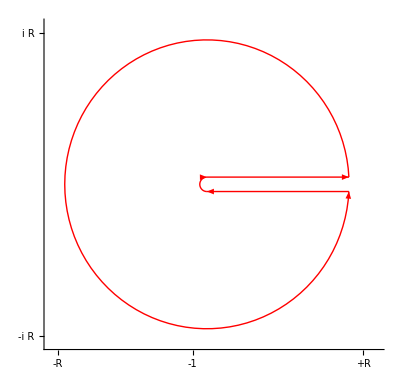

Calcolo su tratto lineare verso X+

lp= 1.4224-0.790368 ⅈ

Calcolo su tratto circolare antiorario

ca= 1.2241+0.0000199968 ⅈ

Calcolo su tratto lineare verso X-

lm= 1.42239+0.790352 ⅈ

Calcolo su tratto circolare orario

co= 2.2143-9.97292×10^-6 ⅈ

Valori approssimati dalle somme di Riemann

lp= 1.4224-0.790368 ⅈ

ca= 1.2241+0.0000199968 ⅈ

lm= 1.42239+0.790352 ⅈ

co= 2.2143-9.97292×10^-6 ⅈ

Valori ottenuti con NIntegrate

lp= 1.42239-0.790365 ⅈ

ca= 1.2241

lm= 1.42239+0.790365 ⅈ

co= 2.2143

Errori

err_lp= 2.82273×10^-6

err_ca= 0.0000199968

err_lm= 0.0000137266

err_co= 9.97849×10^-6

Valore dell'integrale sul contorno chiuso ottenuto con le somme di Riemann= 6.28318-5.87035×10^-6 ⅈ

Valore dell'integrale sul contorno chiuso ottenuto con NIntegrate= 6.28319+0. ⅈ

Errore= 7.04306×10^-6

Residuo nel polo (-1) = 6.12323×10^-17-1. ⅈ

Valore dell'integrale sul contorno chiuso ottenuto col teorema dei residui= 6.28319+3.84734×10^-16 ⅈ

```mathematica
(*
f1[z_]:=z^(p-1)/(z+1) sarebbe sbagliato. Infatti la potenza z^ ha un punto di diramazione in 0; questo rende necessario un branch-cut per rendere univoca la funzione. Il problema e' che la funzione potenza utilizza internamente la funzione Log che restituisce un argomento compreso tra -Pi e Pi. Quindi per default il branch cut e' l'asse delle ascisse negative; ma questo non va' bene perche' viene intersecato dai contorni circolari. E' percio' necessario esprimere la potenza mediante una funzione di log customizzata che restituisca un argomento compreso tra 0 e 2 Pi in modo da avere come branch cut l'asse delle ascisse positive (che non viene attraversato da nessun contorno)
*)

Clear[arg,log]
arg[z_,σ_:-Pi]:=Arg[z Exp[-I (σ+Pi)]]+σ+Pi
log[z_,σ_:-Pi]:=Log[Abs[z]]+I arg[z,σ]

p=0.5;

f1[z_]:=E^((p-1)log[z,0])/(z+1) 
f2[z_]:=z^(p-1)/(z+1)                                               (* normale espressione per calcolo residui *)

eps=0.5 ;                                                                                 (* Se eps<1 il polo (-1) e' interno al contorno *)
cntrLp[t_]:=t+I eps
cntrLm[t_]:=t-I eps

cntrCo[t_]:=eps (Cos[t]+ I Sin[t])

l=10;
r = Sqrt[l^2+eps^2];
cntrCa[t_]:=r (Cos[t]+ I Sin[t])

th=ArcTan[eps/l];

lin[x_]:={Arrowheads[{{0.05,0.5}}],Arrow[Most@x]};
arc[x_]:={Arrowheads[{{0.05,0.5}}],Arrow[Table[x[[1]] {Cos[j],x[[4]] Sin[j]},{j,x[[2]],x[[3]],0.01 (x[[3]]-x[[2]])}]]};
cont[lst_]:=If[#[[-1]]=="line",lin@#,arc@#]&/@lst

Graphics[{Red,cont[{{{0,eps},{l,eps},"line"},{r,th,2 Pi-th,1,"arc"},{{l,-eps},{0,-eps},"line"},{eps,Pi/2,3 Pi/2,-1,"arc"}}],Black,},Axes->True,Ticks->{{{r+1,"+R"},{-1,"-1"},{-r-0.5,"-R"}},{{r+0.5,"i R"},{-r-0.5,"-i R"}}},PlotRange->{{-r-1,r+2},{-r-1,r+1}}]

prec=18;
verb=False;
Print["\n"]
Print["\nCalcolo su tratto lineare verso X+"]
lp=ContourRiemannSum[f1,cntrLp,0,l,prec,verb];
Print["lp= ",lp]
Print["\nCalcolo su tratto circolare antiorario"]
ca=ContourRiemannSum[f1,cntrCa,th,2 Pi-th,prec,verb];
Print["ca= ",ca]
Print["\nCalcolo su tratto lineare verso X-"]
lm=ContourRiemannSum[f1,cntrLm,l,0,prec,verb];
Print["lm= ",lm]
Print["\nCalcolo su tratto circolare orario"]
co=ContourRiemannSum[f1,cntrCo,3 Pi/2,Pi/2,prec,verb];
Print["co= ",co]

Print["\nValori approssimati dalle somme di Riemann"]
Print["lp= ",lp]
Print["ca= ",ca]
Print["lm= ",lm]
Print["co= ",co]

Somma=lp+ca+lm+co;

lpth=NIntegrate[f1[cntrLp[t]]cntrLp'[t],{t,0,l}];
cath=NIntegrate[f1[cntrCa[t]] cntrCa'[t],{t,th,2 Pi-th}];
lmth=NIntegrate[f1[cntrLm[t]]cntrLm'[t],{t,l,0}];
coth=NIntegrate[f1[cntrCo[t]] cntrCo'[t],{t,3Pi/2,Pi/2}];

Print["\nValori ottenuti con NIntegrate"]
Print["lp= ",lpth]
Print["ca= ",cath]
Print["lm= ",lmth]
Print["co= ",coth]

Sommath=lpth+cath+lmth+coth;

Print["\nErrori"]
Print["err_lp= ",Abs[lp-lpth]]
Print["err_ca= ",Abs[ca-cath]]
Print["err_lm= ",Abs[lm-lmth]]
Print["err_co= ",Abs[co-coth]]

Print["\nValore dell'integrale sul contorno chiuso ottenuto con le somme di Riemann= ",Somma]
Print["Valore dell'integrale sul contorno chiuso ottenuto con NIntegrate= ",Sommath]
Print["Errore= ",Abs[Somma-Sommath],"\n"]

Clear[z]
res=Residue[f2[z],{z,-1}];
Print["Residuo nel polo (-1) = ",res]
If [eps>1,res=0]
Print["Valore dell'integrale sul contorno chiuso ottenuto col teorema dei residui= ",2Pi I res,"\n"]
```